```mathematica
steps=Table[t,{t,0,10^3}];
```

```mathematica
selectInterval[steps_,saveFreq_,saveIntervalLength_,saveIntervalDistance_]:=Select[steps,Mod[#,saveFreq]==0&&Mod[Floor[#/saveIntervalLength],saveIntervalDistance/saveIntervalLength]==0&];
```

{0,1,2,3,4,5,6,7,8,9,100,101,102,103,104,105,106,107,108,109,200,201,202,203,204,205,206,207,208,209,300,301,302,303,304,305,306,307,308,309,400,401,402,403,404,405,406,407,408,409,500,501,502,503,504,505,506,507,508,509,600,601,602,603,604,605,606,607,608,609,700,701,702,703,704,705,706,707,708,709,800,801,802,803,804,805,806,807,808,809,900,901,902,903,904,905,906,907,908,909,1000}

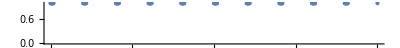

```mathematica
With[{
saveFreq=1,
saveIntervalLength=10,
saveIntervalDistance=100
},selectInterval[steps,saveFreq,saveIntervalLength,saveIntervalDistance]]
%//NumberLinePlot
```

```mathematica
Manipulate[
selectInterval[steps,saveFreq,saveIntervalLength,saveIntervalDistance]//NumberLinePlot,
{saveFreq,1,100,1},
{saveIntervalLength,1,100,1},
{saveIntervalDistance,1,1000}
]
```